## P2.3

### Part b

#### Clear main context

```mathematica
Clear["`*"]
```

#### Solve the equation

```mathematica
sol = NDSolve[{y''[x] + Sin[y[x]] == 1, y[0] ==0, y[3] ==0 }, y, {x, 0, 3}];
```

#### Plot the solution

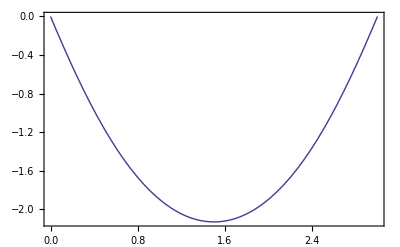

```mathematica
Plot[Evaluate[y[x]/.sol], {x, 0, 3}, Axes->False, Frame->True]
```